```mathematica
Integrate[1/Sqrt[(x-xt)^2 + (y-yt)^2]*1,{x,-1,1},{y,-1,1}]
```

$Aborted

```mathematica
Assuming[{-1≤a≤0},Integrate[1/Sqrt[x^2+y^2 + z^2],{x,a,a+1},{y,-1/2,1/2},{z,-1/2,1/2}]]
```

-ArcSinh[√2 a]+ArcSinh[√2 (1+a)]+ArcTan[a/(√(1/2+a^2))]-ArcTan[(1+a)/(√(3/2+2 a+a^2))]+2 a^2 ArcTan[1/(2 a √(2+4 a^2))]-2 ArcTan[1/(2 (1+a) √(6+8 a+4 a^2))]-4 a ArcTan[1/(2 (1+a) √(6+8 a+4 a^2))]-2 a^2 ArcTan[1/(2 (1+a) √(6+8 a+4 a^2))]+2 a Log[1+4 a^2]-2 Log[5+4 a (2+a)]-2 a Log[5+4 a (2+a)]-4 a Log[1+√(2+4 a^2)]+4 Log[1+√(6+8 a+4 a^2)]+4 a Log[1+√(6+8 a+4 a^2)]

```mathematica
OneD = Assuming[{b>a,b≥0,a≤0},Integrate[1/Sqrt[x^2+y^2 + z^2],{x,a,b},{y,-1/2,1/2},{z,-1/2,1/2}]]
```

2 a^2 ArcCot[2 a √(2+4 a^2)]-2 b^2 ArcCot[2 b √(2+4 b^2)]-ArcSinh[√2 a]+ArcSinh[√2 b]+ArcTan[(√2 a)/(√(1+2 a^2))]-ArcTan[(√2 b)/(√(1+2 b^2))]+2 a Log[1+4 a^2]-4 a Log[1+√(2+4 a^2)]-2 b Log[1+4 b^2]+4 b Log[1+√(2+4 b^2)]

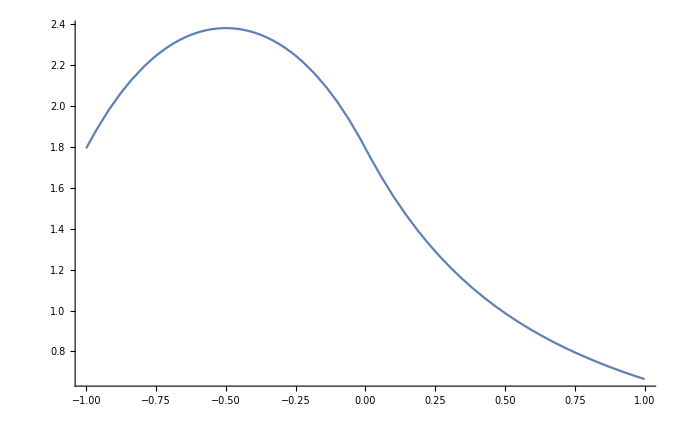

```mathematica
Plot[OneD/.b->a+1,{a,-1,1}]
```

```mathematica
dOneD=D[OneD/.b->a+1,{a,1}]
```

-(√2)/(√(1+2 a^2))+(16 a^2)/(1+4 a^2)+(√2)/(√(1+2 (1+a)^2))-(16 (1+a)^2)/(1+4 (1+a)^2)+(-(2 √2 a^2)/((1+2 a^2)^(3/2))+(√2)/(√(1+2 a^2)))/(1+(2 a^2)/(1+2 a^2))-(16 a^2)/(√(2+4 a^2) (1+√(2+4 a^2)))-(2 a^2 ((8 a^2)/(√(2+4 a^2))+2 √(2+4 a^2)))/(1+4 a^2 (2+4 a^2))-(-(2 √2 (1+a)^2)/((1+2 (1+a)^2)^(3/2))+(√2)/(√(1+2 (1+a)^2)))/(1+(2 (1+a)^2)/(1+2 (1+a)^2))+(16 (1+a)^2)/(√(2+4 (1+a)^2) (1+√(2+4 (1+a)^2)))+(2 (1+a)^2 ((8 (1+a)^2)/(√(2+4 (1+a)^2))+2 √(2+4 (1+a)^2)))/(1+4 (1+a)^2 (2+4 (1+a)^2))+4 a ArcCot[2 a √(2+4 a^2)]-4 (1+a) ArcCot[2 (1+a) √(2+4 (1+a)^2)]+2 Log[1+4 a^2]-2 Log[1+4 (1+a)^2]-4 Log[1+√(2+4 a^2)]+4 Log[1+√(2+4 (1+a)^2)]

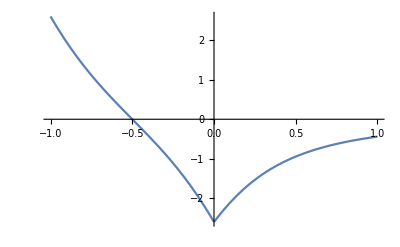

```mathematica
Plot[dOneD,{a,-1,1}]
```

```mathematica
Integrate[1/Sqrt[x^2+y^2 + z^2],{x,-1/2,1/2},{y,-1/2,1/2},{z,-1/2,1/2}]
```

-π/2-2 ArcSinh[1/(√2)]+Log[97+56 √3]

```mathematica
Out[16]*1.0
```

2.380077363979554

```mathematica
Integrate[1/Sqrt[x^2+y^2 + z^2],{x,0,1},{y,-1/2,1/2},{z,-1/2,1/2}]
```

-ArcSinh[√2]-ArcTan[√(2/3)]-2 ArcTan[1/(2 √6)]-2 Log[5]+Log[701+286 √6]

```mathematica
Integrate[1/Sqrt[x^2+y^2 + z^2],{x,0,1},{y,0,1},{z,-1/2,1/2}]
```

1/4 (-8 ArcCot[3]-ArcTan[4/3]+Log[10000])

```mathematica
Out[36]*1.0
```

1.79281

```mathematica
Out[34]*1.0
```

1.42726

```mathematica
Out[19]/.{b->1,a->0.000001}
```

1.79281

```mathematica
Assuming[{b>a,b≥0,a≤0, d>c,d≥0,c≤0},Integrate[1/Sqrt[x^2+y^2 + z^2],{x,a,b},{y,c,d}]]
```

ConditionalExpression[-z ArcTan[(a c)/(z √(a^2+c^2+z^2))]+z ArcTan[(b c)/(z √(b^2+c^2+z^2))]+z ArcTan[(a d)/(z √(a^2+d^2+z^2))]-z ArcTan[(b d)/(z √(b^2+d^2+z^2))]+c Log[a+√(a^2+c^2+z^2)]+a Log[c+√(a^2+c^2+z^2)]-c Log[b+√(b^2+c^2+z^2)]-b Log[c+√(b^2+c^2+z^2)]-d Log[a+√(a^2+d^2+z^2)]-a Log[d+√(a^2+d^2+z^2)]+d Log[b+√(b^2+d^2+z^2)]+b Log[d+√(b^2+d^2+z^2)],c+Re[√(a^2+c^2+z^2)]≥0&&(a≥0||b≤0)&&(√(-c^2+Im[z]^2)∉Reals||a+Re[√(-c^2+Im[z]^2)]≥0||b+Re[√(-c^2+Im[z]^2)]≤0||√(-c^2+Im[z]^2)≤Re[√(z^2+Im[z]^2)])]

```mathematica
Assuming[{b>a,b≥0,a≤0, d>c,d≥0,c≤0},Integrate[1/Sqrt[x^2+y^2 + z^2],{x,a,b},{y,c,d},{z,-1/2,1/2}]]
```

ConditionalExpression[-c^2 ArcTan[a/(c √(1+4 a^2+4 c^2))]-a^2 ArcTan[c/(a √(1+4 a^2+4 c^2))]+c^2 ArcTan[b/(c √(1+4 b^2+4 c^2))]+b^2 ArcTan[c/(b √(1+4 b^2+4 c^2))]+d^2 ArcTan[a/(d √(1+4 a^2+4 d^2))]+a^2 ArcTan[d/(a √(1+4 a^2+4 d^2))]-d^2 ArcTan[b/(d √(1+4 b^2+4 d^2))]-b^2 ArcTan[d/(b √(1+4 b^2+4 d^2))]-a c Log[4]+b c Log[4]+a d Log[4]-b d Log[4]-a c Log[a^2+c^2]+b c Log[b^2+c^2]+2 c Log[1+4 c^2]+2 a c Log[1+√(1+4 a^2+4 c^2)]-2 c Log[-2 a+√(1+4 a^2+4 c^2)]-c Log[2 a+√(1+4 a^2+4 c^2)]+a Log[2 c+√(1+4 a^2+4 c^2)]-2 b c Log[1+√(1+4 b^2+4 c^2)]-c Log[2 b+√(1+4 b^2+4 c^2)]-b Log[2 c+√(1+4 b^2+4 c^2)]-1/8 ⅈ Log[(2 a-ⅈ (1+4 c^2+2 c √(1+4 a^2+4 c^2)))/(-ⅈ+2 a)]+1/8 ⅈ Log[(2 a+ⅈ (1+4 c^2+2 c √(1+4 a^2+4 c^2)))/(ⅈ+2 a)]+1/8 ⅈ Log[(2 b-ⅈ (1+4 c^2+2 c √(1+4 b^2+4 c^2)))/(-ⅈ+2 b)]-1/8 ⅈ Log[(2 b+ⅈ (1+4 c^2+2 c √(1+4 b^2+4 c^2)))/(ⅈ+2 b)]+a d Log[a^2+d^2]-b d Log[b^2+d^2]-d Log[1+4 d^2]-2 a d Log[1+√(1+4 a^2+4 d^2)]+d Log[-2 a+√(1+4 a^2+4 d^2)]-a Log[2 d+√(1+4 a^2+4 d^2)]+2 b d Log[1+√(1+4 b^2+4 d^2)]+d Log[2 b+√(1+4 b^2+4 d^2)]+b Log[2 d+√(1+4 b^2+4 d^2)]+1/8 ⅈ Log[(2 a-ⅈ (1+4 d^2+2 d √(1+4 a^2+4 d^2)))/(-ⅈ+2 a)]-1/8 ⅈ Log[(2 a+ⅈ (1+4 d^2+2 d √(1+4 a^2+4 d^2)))/(ⅈ+2 a)]-1/8 ⅈ Log[(2 b-ⅈ (1+4 d^2+2 d √(1+4 b^2+4 d^2)))/(-ⅈ+2 b)]+1/8 ⅈ Log[(2 b+ⅈ (1+4 d^2+2 d √(1+4 b^2+4 d^2)))/(ⅈ+2 b)],a<0]

```mathematica
Plot3D[Normal[Out[51]]/.{b->a+1,d->c+1},{a,-1,0},{c,-1,0}]
```

-Graphics3D-

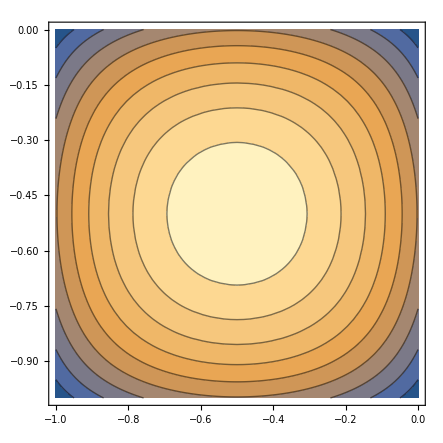

```mathematica
ContourPlot[Normal[Out[51]]/.{b->a+1,d->c+1},{a,-1,0},{c,-1,0}]
```

```mathematica
Assuming[{b>a,b>0,a<0, d>c,d>0,c<0, f>e, f>0, e<0},Integrate[1/Sqrt[x^2+y^2 + z^2],{x,a,b},{y,c,d},{z,e,f}]]
```

e (2 a-2 b-2 e ArcTan[a/e]+2 e ArcTan[b/e]-a Log[a^2+e^2]+b Log[b^2+e^2])+e (-a+b+e ArcTan[a/e]-e ArcTan[b/e]+e ArcTan[(a c)/(e √(a^2+c^2+e^2))]-e ArcTan[(b c)/(e √(b^2+c^2+e^2))]-c Log[c^2+e^2]+c Log[-a+√(a^2+c^2+e^2)]+a Log[-c+√(a^2+c^2+e^2)]+c Log[b+√(b^2+c^2+e^2)]-b Log[-c+√(b^2+c^2+e^2)])+e (-a+b+e ArcTan[a/e]-e ArcTan[b/e]-e ArcTan[(a d)/(e √(a^2+d^2+e^2))]+e ArcTan[(b d)/(e √(b^2+d^2+e^2))]+d Log[d^2+e^2]-d Log[-a+√(a^2+d^2+e^2)]+a Log[d+√(a^2+d^2+e^2)]-d Log[b+√(b^2+d^2+e^2)]-b Log[d+√(b^2+d^2+e^2)])+1/4 (4 c^2 π+4 e^2 π+2 a^2 ArcTan[(c e)/(a √(a^2+c^2+e^2))]-2 b^2 ArcTan[(c e)/(b √(b^2+c^2+e^2))]+4 c e Log[c^2+e^2]-4 c e Log[-a+√(a^2+c^2+e^2)]-ⅈ e^2 Log[(-ⅈ c^2+(a-ⅈ e) e-ⅈ c √(a^2+c^2+e^2))/(a-ⅈ e)]+ⅈ e^2 Log[(ⅈ c^2+(a+ⅈ e) e+ⅈ c √(a^2+c^2+e^2))/(a+ⅈ e)]-4 c e Log[b+√(b^2+c^2+e^2)]+ⅈ e^2 Log[(-ⅈ c^2+(b-ⅈ e) e-ⅈ c √(b^2+c^2+e^2))/(b-ⅈ e)]-ⅈ e^2 Log[(ⅈ c^2+(b+ⅈ e) e+ⅈ c √(b^2+c^2+e^2))/(b+ⅈ e)]-ⅈ c^2 Log[(a c-ⅈ (c^2+e (e+√(a^2+c^2+e^2))))/(a-ⅈ c)]+ⅈ c^2 Log[(a c+ⅈ (c^2+e (e+√(a^2+c^2+e^2))))/(a+ⅈ c)]+ⅈ c^2 Log[(b c-ⅈ (c^2+e (e+√(b^2+c^2+e^2))))/(b-ⅈ c)]-ⅈ c^2 Log[(b c+ⅈ (c^2+e (e+√(b^2+c^2+e^2))))/(b+ⅈ c)])+1/4 (4 e^2 π-2 a^2 ArcTan[(d e)/(a √(a^2+d^2+e^2))]+2 b^2 ArcTan[(d e)/(b √(b^2+d^2+e^2))]-4 d e Log[d^2+e^2]+4 d e Log[-a+√(a^2+d^2+e^2)]+ⅈ e^2 Log[(-ⅈ d^2+(a-ⅈ e) e-ⅈ d √(a^2+d^2+e^2))/(a-ⅈ e)]-ⅈ e^2 Log[(ⅈ d^2+(a+ⅈ e) e+ⅈ d √(a^2+d^2+e^2))/(a+ⅈ e)]+4 d e Log[b+√(b^2+d^2+e^2)]-ⅈ e^2 Log[(-ⅈ d^2+(b-ⅈ e) e-ⅈ d √(b^2+d^2+e^2))/(b-ⅈ e)]+ⅈ e^2 Log[(ⅈ d^2+(b+ⅈ e) e+ⅈ d √(b^2+d^2+e^2))/(b+ⅈ e)]+ⅈ d^2 Log[(a d-ⅈ (d^2+e (e+√(a^2+d^2+e^2))))/(a-ⅈ d)]-ⅈ d^2 Log[(a d+ⅈ (d^2+e (e+√(a^2+d^2+e^2))))/(a+ⅈ d)]-ⅈ d^2 Log[(b d-ⅈ (d^2+e (e+√(b^2+d^2+e^2))))/(b-ⅈ d)]+ⅈ d^2 Log[(b d+ⅈ (d^2+e (e+√(b^2+d^2+e^2))))/(b+ⅈ d)])+f (-2 a+2 b+2 f ArcTan[a/f]-2 f ArcTan[b/f]+a Log[a^2+f^2]-b Log[b^2+f^2])-f (-a+b+f ArcTan[a/f]-f ArcTan[b/f]+f ArcTan[(a c)/(f √(a^2+c^2+f^2))]-f ArcTan[(b c)/(f √(b^2+c^2+f^2))]-c Log[c^2+f^2]+c Log[-a+√(a^2+c^2+f^2)]+a Log[-c+√(a^2+c^2+f^2)]+c Log[b+√(b^2+c^2+f^2)]-b Log[-c+√(b^2+c^2+f^2)])+c (c ArcTan[(a e)/(c √(a^2+c^2+e^2))]-c ArcTan[(b e)/(c √(b^2+c^2+e^2))]-c ArcTan[(a f)/(c √(a^2+c^2+f^2))]+c ArcTan[(b f)/(c √(b^2+c^2+f^2))]-e Log[c^2+e^2]+e Log[-a+√(a^2+c^2+e^2)]+e Log[b+√(b^2+c^2+e^2)]+f Log[c^2+f^2]-f Log[-a+√(a^2+c^2+f^2)]+a Log[(f+√(a^2+c^2+f^2))/(e+√(a^2+c^2+e^2))]-f Log[b+√(b^2+c^2+f^2)]-b Log[(f+√(b^2+c^2+f^2))/(e+√(b^2+c^2+e^2))])+f (a-b-f ArcTan[a/f]+f ArcTan[b/f]+f ArcTan[(a d)/(f √(a^2+d^2+f^2))]-f ArcTan[(b d)/(f √(b^2+d^2+f^2))]-d Log[d^2+f^2]+d Log[-a+√(a^2+d^2+f^2)]-a Log[d+√(a^2+d^2+f^2)]+d Log[b+√(b^2+d^2+f^2)]+b Log[d+√(b^2+d^2+f^2)])+d (-d ArcTan[(a e)/(d √(a^2+d^2+e^2))]+d ArcTan[(b e)/(d √(b^2+d^2+e^2))]+d ArcTan[(a f)/(d √(a^2+d^2+f^2))]-d ArcTan[(b f)/(d √(b^2+d^2+f^2))]+e Log[d^2+e^2]-e Log[-a+√(a^2+d^2+e^2)]-e Log[b+√(b^2+d^2+e^2)]-f Log[d^2+f^2]+f Log[-a+√(a^2+d^2+f^2)]-a Log[(f+√(a^2+d^2+f^2))/(e+√(a^2+d^2+e^2))]+f Log[b+√(b^2+d^2+f^2)]+b Log[(f+√(b^2+d^2+f^2))/(e+√(b^2+d^2+e^2))])+1/4 (4 c^2 π-2 a^2 ArcTan[(c f)/(a √(a^2+c^2+f^2))]+2 b^2 ArcTan[(c f)/(b √(b^2+c^2+f^2))]-4 c f Log[c^2+f^2]+4 c f Log[-a+√(a^2+c^2+f^2)]+ⅈ f^2 Log[(-ⅈ c^2+(a-ⅈ f) f-ⅈ c √(a^2+c^2+f^2))/(a-ⅈ f)]-ⅈ f^2 Log[(ⅈ c^2+(a+ⅈ f) f+ⅈ c √(a^2+c^2+f^2))/(a+ⅈ f)]+4 c f Log[b+√(b^2+c^2+f^2)]-ⅈ f^2 Log[(-ⅈ c^2+(b-ⅈ f) f-ⅈ c √(b^2+c^2+f^2))/(b-ⅈ f)]+ⅈ f^2 Log[(ⅈ c^2+(b+ⅈ f) f+ⅈ c √(b^2+c^2+f^2))/(b+ⅈ f)]+ⅈ c^2 Log[(a c-ⅈ (c^2+f (f+√(a^2+c^2+f^2))))/(a-ⅈ c)]-ⅈ c^2 Log[(a c+ⅈ (c^2+f (f+√(a^2+c^2+f^2))))/(a+ⅈ c)]-ⅈ c^2 Log[(b c-ⅈ (c^2+f (f+√(b^2+c^2+f^2))))/(b-ⅈ c)]+ⅈ c^2 Log[(b c+ⅈ (c^2+f (f+√(b^2+c^2+f^2))))/(b+ⅈ c)])+1/4 (2 a^2 ArcTan[(d f)/(a √(a^2+d^2+f^2))]-2 b^2 ArcTan[(d f)/(b √(b^2+d^2+f^2))]-ⅈ (4 ⅈ d f Log[d^2+f^2]-4 ⅈ d f Log[-a+√(a^2+d^2+f^2)]+f^2 Log[(-ⅈ d^2+(a-ⅈ f) f-ⅈ d √(a^2+d^2+f^2))/(a-ⅈ f)]-f^2 Log[(ⅈ d^2+(a+ⅈ f) f+ⅈ d √(a^2+d^2+f^2))/(a+ⅈ f)]-4 ⅈ d f Log[b+√(b^2+d^2+f^2)]-f^2 Log[(-ⅈ d^2+(b-ⅈ f) f-ⅈ d √(b^2+d^2+f^2))/(b-ⅈ f)]+f^2 Log[(ⅈ d^2+(b+ⅈ f) f+ⅈ d √(b^2+d^2+f^2))/(b+ⅈ f)]+d^2 Log[(a d-ⅈ (d^2+f (f+√(a^2+d^2+f^2))))/(a-ⅈ d)]-d^2 Log[(a d+ⅈ (d^2+f (f+√(a^2+d^2+f^2))))/(a+ⅈ d)]-d^2 Log[(b d-ⅈ (d^2+f (f+√(b^2+d^2+f^2))))/(b-ⅈ d)]+d^2 Log[(b d+ⅈ (d^2+f (f+√(b^2+d^2+f^2))))/(b+ⅈ d)]))

```mathematica
full:=e (2 a-2 b-2 e ArcTan[a/e]+2 e ArcTan[b/e]-a Log[a^2+e^2]+b Log[b^2+e^2])+e (-a+b+e ArcTan[a/e]-e ArcTan[b/e]+e ArcTan[(a c)/(e √(a^2+c^2+e^2))]-e ArcTan[(b c)/(e √(b^2+c^2+e^2))]-c Log[c^2+e^2]+c Log[-a+√(a^2+c^2+e^2)]+a Log[-c+√(a^2+c^2+e^2)]+c Log[b+√(b^2+c^2+e^2)]-b Log[-c+√(b^2+c^2+e^2)])+e (-a+b+e ArcTan[a/e]-e ArcTan[b/e]-e ArcTan[(a d)/(e √(a^2+d^2+e^2))]+e ArcTan[(b d)/(e √(b^2+d^2+e^2))]+d Log[d^2+e^2]-d Log[-a+√(a^2+d^2+e^2)]+a Log[d+√(a^2+d^2+e^2)]-d Log[b+√(b^2+d^2+e^2)]-b Log[d+√(b^2+d^2+e^2)])+1/4 (4 c^2 π+4 e^2 π+2 a^2 ArcTan[(c e)/(a √(a^2+c^2+e^2))]-2 b^2 ArcTan[(c e)/(b √(b^2+c^2+e^2))]+4 c e Log[c^2+e^2]-4 c e Log[-a+√(a^2+c^2+e^2)]-ⅈ e^2 Log[(-ⅈ c^2+(a-ⅈ e) e-ⅈ c √(a^2+c^2+e^2))/(a-ⅈ e)]+ⅈ e^2 Log[(ⅈ c^2+(a+ⅈ e) e+ⅈ c √(a^2+c^2+e^2))/(a+ⅈ e)]-4 c e Log[b+√(b^2+c^2+e^2)]+ⅈ e^2 Log[(-ⅈ c^2+(b-ⅈ e) e-ⅈ c √(b^2+c^2+e^2))/(b-ⅈ e)]-ⅈ e^2 Log[(ⅈ c^2+(b+ⅈ e) e+ⅈ c √(b^2+c^2+e^2))/(b+ⅈ e)]-ⅈ c^2 Log[(a c-ⅈ (c^2+e (e+√(a^2+c^2+e^2))))/(a-ⅈ c)]+ⅈ c^2 Log[(a c+ⅈ (c^2+e (e+√(a^2+c^2+e^2))))/(a+ⅈ c)]+ⅈ c^2 Log[(b c-ⅈ (c^2+e (e+√(b^2+c^2+e^2))))/(b-ⅈ c)]-ⅈ c^2 Log[(b c+ⅈ (c^2+e (e+√(b^2+c^2+e^2))))/(b+ⅈ c)])+1/4 (4 e^2 π-2 a^2 ArcTan[(d e)/(a √(a^2+d^2+e^2))]+2 b^2 ArcTan[(d e)/(b √(b^2+d^2+e^2))]-4 d e Log[d^2+e^2]+4 d e Log[-a+√(a^2+d^2+e^2)]+ⅈ e^2 Log[(-ⅈ d^2+(a-ⅈ e) e-ⅈ d √(a^2+d^2+e^2))/(a-ⅈ e)]-ⅈ e^2 Log[(ⅈ d^2+(a+ⅈ e) e+ⅈ d √(a^2+d^2+e^2))/(a+ⅈ e)]+4 d e Log[b+√(b^2+d^2+e^2)]-ⅈ e^2 Log[(-ⅈ d^2+(b-ⅈ e) e-ⅈ d √(b^2+d^2+e^2))/(b-ⅈ e)]+ⅈ e^2 Log[(ⅈ d^2+(b+ⅈ e) e+ⅈ d √(b^2+d^2+e^2))/(b+ⅈ e)]+ⅈ d^2 Log[(a d-ⅈ (d^2+e (e+√(a^2+d^2+e^2))))/(a-ⅈ d)]-ⅈ d^2 Log[(a d+ⅈ (d^2+e (e+√(a^2+d^2+e^2))))/(a+ⅈ d)]-ⅈ d^2 Log[(b d-ⅈ (d^2+e (e+√(b^2+d^2+e^2))))/(b-ⅈ d)]+ⅈ d^2 Log[(b d+ⅈ (d^2+e (e+√(b^2+d^2+e^2))))/(b+ⅈ d)])+f (-2 a+2 b+2 f ArcTan[a/f]-2 f ArcTan[b/f]+a Log[a^2+f^2]-b Log[b^2+f^2])-f (-a+b+f ArcTan[a/f]-f ArcTan[b/f]+f ArcTan[(a c)/(f √(a^2+c^2+f^2))]-f ArcTan[(b c)/(f √(b^2+c^2+f^2))]-c Log[c^2+f^2]+c Log[-a+√(a^2+c^2+f^2)]+a Log[-c+√(a^2+c^2+f^2)]+c Log[b+√(b^2+c^2+f^2)]-b Log[-c+√(b^2+c^2+f^2)])+c (c ArcTan[(a e)/(c √(a^2+c^2+e^2))]-c ArcTan[(b e)/(c √(b^2+c^2+e^2))]-c ArcTan[(a f)/(c √(a^2+c^2+f^2))]+c ArcTan[(b f)/(c √(b^2+c^2+f^2))]-e Log[c^2+e^2]+e Log[-a+√(a^2+c^2+e^2)]+e Log[b+√(b^2+c^2+e^2)]+f Log[c^2+f^2]-f Log[-a+√(a^2+c^2+f^2)]+a Log[(f+√(a^2+c^2+f^2))/(e+√(a^2+c^2+e^2))]-f Log[b+√(b^2+c^2+f^2)]-b Log[(f+√(b^2+c^2+f^2))/(e+√(b^2+c^2+e^2))])+f (a-b-f ArcTan[a/f]+f ArcTan[b/f]+f ArcTan[(a d)/(f √(a^2+d^2+f^2))]-f ArcTan[(b d)/(f √(b^2+d^2+f^2))]-d Log[d^2+f^2]+d Log[-a+√(a^2+d^2+f^2)]-a Log[d+√(a^2+d^2+f^2)]+d Log[b+√(b^2+d^2+f^2)]+b Log[d+√(b^2+d^2+f^2)])+d (-d ArcTan[(a e)/(d √(a^2+d^2+e^2))]+d ArcTan[(b e)/(d √(b^2+d^2+e^2))]+d ArcTan[(a f)/(d √(a^2+d^2+f^2))]-d ArcTan[(b f)/(d √(b^2+d^2+f^2))]+e Log[d^2+e^2]-e Log[-a+√(a^2+d^2+e^2)]-e Log[b+√(b^2+d^2+e^2)]-f Log[d^2+f^2]+f Log[-a+√(a^2+d^2+f^2)]-a Log[(f+√(a^2+d^2+f^2))/(e+√(a^2+d^2+e^2))]+f Log[b+√(b^2+d^2+f^2)]+b Log[(f+√(b^2+d^2+f^2))/(e+√(b^2+d^2+e^2))])+1/4 (4 c^2 π-2 a^2 ArcTan[(c f)/(a √(a^2+c^2+f^2))]+2 b^2 ArcTan[(c f)/(b √(b^2+c^2+f^2))]-4 c f Log[c^2+f^2]+4 c f Log[-a+√(a^2+c^2+f^2)]+ⅈ f^2 Log[(-ⅈ c^2+(a-ⅈ f) f-ⅈ c √(a^2+c^2+f^2))/(a-ⅈ f)]-ⅈ f^2 Log[(ⅈ c^2+(a+ⅈ f) f+ⅈ c √(a^2+c^2+f^2))/(a+ⅈ f)]+4 c f Log[b+√(b^2+c^2+f^2)]-ⅈ f^2 Log[(-ⅈ c^2+(b-ⅈ f) f-ⅈ c √(b^2+c^2+f^2))/(b-ⅈ f)]+ⅈ f^2 Log[(ⅈ c^2+(b+ⅈ f) f+ⅈ c √(b^2+c^2+f^2))/(b+ⅈ f)]+ⅈ c^2 Log[(a c-ⅈ (c^2+f (f+√(a^2+c^2+f^2))))/(a-ⅈ c)]-ⅈ c^2 Log[(a c+ⅈ (c^2+f (f+√(a^2+c^2+f^2))))/(a+ⅈ c)]-ⅈ c^2 Log[(b c-ⅈ (c^2+f (f+√(b^2+c^2+f^2))))/(b-ⅈ c)]+ⅈ c^2 Log[(b c+ⅈ (c^2+f (f+√(b^2+c^2+f^2))))/(b+ⅈ c)])+1/4 (2 a^2 ArcTan[(d f)/(a √(a^2+d^2+f^2))]-2 b^2 ArcTan[(d f)/(b √(b^2+d^2+f^2))]-ⅈ (4 ⅈ d f Log[d^2+f^2]-4 ⅈ d f Log[-a+√(a^2+d^2+f^2)]+f^2 Log[(-ⅈ d^2+(a-ⅈ f) f-ⅈ d √(a^2+d^2+f^2))/(a-ⅈ f)]-f^2 Log[(ⅈ d^2+(a+ⅈ f) f+ⅈ d √(a^2+d^2+f^2))/(a+ⅈ f)]-4 ⅈ d f Log[b+√(b^2+d^2+f^2)]-f^2 Log[(-ⅈ d^2+(b-ⅈ f) f-ⅈ d √(b^2+d^2+f^2))/(b-ⅈ f)]+f^2 Log[(ⅈ d^2+(b+ⅈ f) f+ⅈ d √(b^2+d^2+f^2))/(b+ⅈ f)]+d^2 Log[(a d-ⅈ (d^2+f (f+√(a^2+d^2+f^2))))/(a-ⅈ d)]-d^2 Log[(a d+ⅈ (d^2+f (f+√(a^2+d^2+f^2))))/(a+ⅈ d)]-d^2 Log[(b d-ⅈ (d^2+f (f+√(b^2+d^2+f^2))))/(b-ⅈ d)]+d^2 Log[(b d+ⅈ (d^2+f (f+√(b^2+d^2+f^2))))/(b+ⅈ d)]))
```

```mathematica
FullSimplify[full]
```

1/4 (4 e^2 ArcTan[(a c)/(e √(a^2+c^2+e^2))]-4 e^2 ArcTan[(b c)/(e √(b^2+c^2+e^2))]-4 e^2 ArcTan[(a d)/(e √(a^2+d^2+e^2))]+4 e^2 ArcTan[(b d)/(e √(b^2+d^2+e^2))]+2 (2 c^2 (ArcTan[(a e)/(c √(a^2+c^2+e^2))]-ArcTan[(b e)/(c √(b^2+c^2+e^2))]-ArcTan[(a f)/(c √(a^2+c^2+f^2))]+ArcTan[(b f)/(c √(b^2+c^2+f^2))])+a^2 (ArcTan[(c e)/(a √(a^2+c^2+e^2))]-ArcTan[(d e)/(a √(a^2+d^2+e^2))]-ArcTan[(c f)/(a √(a^2+c^2+f^2))]+ArcTan[(d f)/(a √(a^2+d^2+f^2))])+2 (2 (c^2+e^2) π+f^2 (-ArcTan[(a c)/(f √(a^2+c^2+f^2))]+ArcTan[(b c)/(f √(b^2+c^2+f^2))]+ArcTan[(a d)/(f √(a^2+d^2+f^2))]-ArcTan[(b d)/(f √(b^2+d^2+f^2))])+d^2 (-ArcTan[(a e)/(d √(a^2+d^2+e^2))]+ArcTan[(b e)/(d √(b^2+d^2+e^2))]+ArcTan[(a f)/(d √(a^2+d^2+f^2))]-ArcTan[(b f)/(d √(b^2+d^2+f^2))]))+b^2 (-ArcTan[(c e)/(b √(b^2+c^2+e^2))]+ArcTan[(d e)/(b √(b^2+d^2+e^2))]+ArcTan[(c f)/(b √(b^2+c^2+f^2))]-ArcTan[(d f)/(b √(b^2+d^2+f^2))]))-4 a e Log[a^2+e^2]+4 b e Log[b^2+e^2]-4 c e Log[c^2+e^2]+4 d e Log[d^2+e^2]+4 c e Log[-a+√(a^2+c^2+e^2)]+4 a e Log[-c+√(a^2+c^2+e^2)]+4 c e Log[b+√(b^2+c^2+e^2)]-4 b e Log[-c+√(b^2+c^2+e^2)]-4 d e Log[-a+√(a^2+d^2+e^2)]+4 a e Log[d+√(a^2+d^2+e^2)]-4 d e Log[b+√(b^2+d^2+e^2)]-4 b e Log[d+√(b^2+d^2+e^2)]-ⅈ e^2 Log[((a-ⅈ e) e-ⅈ c (c+√(a^2+c^2+e^2)))/(a-ⅈ e)]+ⅈ e^2 Log[((a+ⅈ e) e+ⅈ c (c+√(a^2+c^2+e^2)))/(a+ⅈ e)]-ⅈ c^2 Log[(ⅈ a c+c^2+e (e+√(a^2+c^2+e^2)))/(ⅈ a+c)]+ⅈ e^2 Log[((b-ⅈ e) e-ⅈ c (c+√(b^2+c^2+e^2)))/(b-ⅈ e)]-ⅈ e^2 Log[((b+ⅈ e) e+ⅈ c (c+√(b^2+c^2+e^2)))/(b+ⅈ e)]+ⅈ c^2 Log[(ⅈ b c+c^2+e (e+√(b^2+c^2+e^2)))/(ⅈ b+c)]+ⅈ e^2 Log[((a-ⅈ e) e-ⅈ d (d+√(a^2+d^2+e^2)))/(a-ⅈ e)]-ⅈ e^2 Log[((a+ⅈ e) e+ⅈ d (d+√(a^2+d^2+e^2)))/(a+ⅈ e)]+ⅈ d^2 Log[(ⅈ a d+d^2+e (e+√(a^2+d^2+e^2)))/(ⅈ a+d)]-ⅈ e^2 Log[((b-ⅈ e) e-ⅈ d (d+√(b^2+d^2+e^2)))/(b-ⅈ e)]+ⅈ e^2 Log[((b+ⅈ e) e+ⅈ d (d+√(b^2+d^2+e^2)))/(b+ⅈ e)]-ⅈ d^2 Log[(ⅈ b d+d^2+e (e+√(b^2+d^2+e^2)))/(ⅈ b+d)]+ⅈ c^2 Log[(a c+ⅈ (c^2+e (e+√(a^2+c^2+e^2))))/(a+ⅈ c)]-ⅈ c^2 Log[(b c+ⅈ (c^2+e (e+√(b^2+c^2+e^2))))/(b+ⅈ c)]-ⅈ d^2 Log[(a d+ⅈ (d^2+e (e+√(a^2+d^2+e^2))))/(a+ⅈ d)]+ⅈ d^2 Log[(b d+ⅈ (d^2+e (e+√(b^2+d^2+e^2))))/(b+ⅈ d)]+4 a f Log[a^2+f^2]-4 b f Log[b^2+f^2]+4 c f Log[c^2+f^2]-4 d f Log[d^2+f^2]-4 c f Log[-a+√(a^2+c^2+f^2)]-4 a f Log[-c+√(a^2+c^2+f^2)]+4 a c Log[(f+√(a^2+c^2+f^2))/(e+√(a^2+c^2+e^2))]-4 c f Log[b+√(b^2+c^2+f^2)]+4 b f Log[-c+√(b^2+c^2+f^2)]-4 b c Log[(f+√(b^2+c^2+f^2))/(e+√(b^2+c^2+e^2))]+4 d f Log[-a+√(a^2+d^2+f^2)]-4 a f Log[d+√(a^2+d^2+f^2)]-4 a d Log[(f+√(a^2+d^2+f^2))/(e+√(a^2+d^2+e^2))]+4 d f Log[b+√(b^2+d^2+f^2)]+4 b f Log[d+√(b^2+d^2+f^2)]+4 b d Log[(f+√(b^2+d^2+f^2))/(e+√(b^2+d^2+e^2))]+ⅈ f^2 Log[((a-ⅈ f) f-ⅈ c (c+√(a^2+c^2+f^2)))/(a-ⅈ f)]-ⅈ f^2 Log[((a+ⅈ f) f+ⅈ c (c+√(a^2+c^2+f^2)))/(a+ⅈ f)]+ⅈ c^2 Log[(ⅈ a c+c^2+f (f+√(a^2+c^2+f^2)))/(ⅈ a+c)]-ⅈ f^2 Log[((b-ⅈ f) f-ⅈ c (c+√(b^2+c^2+f^2)))/(b-ⅈ f)]+ⅈ f^2 Log[((b+ⅈ f) f+ⅈ c (c+√(b^2+c^2+f^2)))/(b+ⅈ f)]-ⅈ c^2 Log[(ⅈ b c+c^2+f (f+√(b^2+c^2+f^2)))/(ⅈ b+c)]-ⅈ f^2 Log[((a-ⅈ f) f-ⅈ d (d+√(a^2+d^2+f^2)))/(a-ⅈ f)]+ⅈ f^2 Log[((a+ⅈ f) f+ⅈ d (d+√(a^2+d^2+f^2)))/(a+ⅈ f)]-ⅈ d^2 Log[(ⅈ a d+d^2+f (f+√(a^2+d^2+f^2)))/(ⅈ a+d)]+ⅈ f^2 Log[((b-ⅈ f) f-ⅈ d (d+√(b^2+d^2+f^2)))/(b-ⅈ f)]-ⅈ f^2 Log[((b+ⅈ f) f+ⅈ d (d+√(b^2+d^2+f^2)))/(b+ⅈ f)]+ⅈ d^2 Log[(ⅈ b d+d^2+f (f+√(b^2+d^2+f^2)))/(ⅈ b+d)]-ⅈ c^2 Log[(a c+ⅈ (c^2+f (f+√(a^2+c^2+f^2))))/(a+ⅈ c)]+ⅈ c^2 Log[(b c+ⅈ (c^2+f (f+√(b^2+c^2+f^2))))/(b+ⅈ c)]+ⅈ d^2 Log[(a d+ⅈ (d^2+f (f+√(a^2+d^2+f^2))))/(a+ⅈ d)]-ⅈ d^2 Log[(b d+ⅈ (d^2+f (f+√(b^2+d^2+f^2))))/(b+ⅈ d)])

```mathematica
FortranForm[Out[2]]
```

(4*e**2*ArcTan((a*c)/(e*Sqrt(a**2 + c**2 + e**2))) - 4*e**2*ArcTan((b*c)/(e*Sqrt(b**2 + c**2 + e**2))) - 4*e**2*ArcTan((a*d)/(e*Sqrt(a**2 + d**2 + e**2))) + 4*e**2*ArcTan((b*d)/(e*Sqrt(b**2 + d**2 + e**2))) + 
     -    2*(2*c**2*(ArcTan((a*e)/(c*Sqrt(a**2 + c**2 + e**2))) - ArcTan((b*e)/(c*Sqrt(b**2 + c**2 + e**2))) - ArcTan((a*f)/(c*Sqrt(a**2 + c**2 + f**2))) + ArcTan((b*f)/(c*Sqrt(b**2 + c**2 + f**2)))) + 
     -       a**2*(ArcTan((c*e)/(a*Sqrt(a**2 + c**2 + e**2))) - ArcTan((d*e)/(a*Sqrt(a**2 + d**2 + e**2))) - ArcTan((c*f)/(a*Sqrt(a**2 + c**2 + f**2))) + ArcTan((d*f)/(a*Sqrt(a**2 + d**2 + f**2)))) + 
     -       2*(2*(c**2 + e**2)*Pi + f**2*(-ArcTan((a*c)/(f*Sqrt(a**2 + c**2 + f**2))) + ArcTan((b*c)/(f*Sqrt(b**2 + c**2 + f**2))) + ArcTan((a*d)/(f*Sqrt(a**2 + d**2 + f**2))) - ArcTan((b*d)/(f*Sqrt(b**2 + d**2 + f**2)))) + 
     -          d**2*(-ArcTan((a*e)/(d*Sqrt(a**2 + d**2 + e**2))) + ArcTan((b*e)/(d*Sqrt(b**2 + d**2 + e**2))) + ArcTan((a*f)/(d*Sqrt(a**2 + d**2 + f**2))) - ArcTan((b*f)/(d*Sqrt(b**2 + d**2 + f**2))))) + 
     -       b**2*(-ArcTan((c*e)/(b*Sqrt(b**2 + c**2 + e**2))) + ArcTan((d*e)/(b*Sqrt(b**2 + d**2 + e**2))) + ArcTan((c*f)/(b*Sqrt(b**2 + c**2 + f**2))) - ArcTan((d*f)/(b*Sqrt(b**2 + d**2 + f**2))))) - 
     -    4*a*e*Log(a**2 + e**2) + 4*b*e*Log(b**2 + e**2) - 4*c*e*Log(c**2 + e**2) + 4*d*e*Log(d**2 + e**2) + 4*c*e*Log(-a + Sqrt(a**2 + c**2 + e**2)) + 4*a*e*Log(-c + Sqrt(a**2 + c**2 + e**2)) + 
     -    4*c*e*Log(b + Sqrt(b**2 + c**2 + e**2)) - 4*b*e*Log(-c + Sqrt(b**2 + c**2 + e**2)) - 4*d*e*Log(-a + Sqrt(a**2 + d**2 + e**2)) + 4*a*e*Log(d + Sqrt(a**2 + d**2 + e**2)) - 4*d*e*Log(b + Sqrt(b**2 + d**2 + e**2)) - 
     -    4*b*e*Log(d + Sqrt(b**2 + d**2 + e**2)) - (0,1)*e**2*Log(((a - (0,1)*e)*e - (0,1)*c*(c + Sqrt(a**2 + c**2 + e**2)))/(a - (0,1)*e)) + 
     -    (0,1)*e**2*Log(((a + (0,1)*e)*e + (0,1)*c*(c + Sqrt(a**2 + c**2 + e**2)))/(a + (0,1)*e)) - (0,1)*c**2*Log(((0,1)*a*c + c**2 + e*(e + Sqrt(a**2 + c**2 + e**2)))/((0,1)*a + c)) + 
     -    (0,1)*e**2*Log(((b - (0,1)*e)*e - (0,1)*c*(c + Sqrt(b**2 + c**2 + e**2)))/(b - (0,1)*e)) - (0,1)*e**2*Log(((b + (0,1)*e)*e + (0,1)*c*(c + Sqrt(b**2 + c**2 + e**2)))/(b + (0,1)*e)) + 
     -    (0,1)*c**2*Log(((0,1)*b*c + c**2 + e*(e + Sqrt(b**2 + c**2 + e**2)))/((0,1)*b + c)) + (0,1)*e**2*Log(((a - (0,1)*e)*e - (0,1)*d*(d + Sqrt(a**2 + d**2 + e**2)))/(a - (0,1)*e)) - 
     -    (0,1)*e**2*Log(((a + (0,1)*e)*e + (0,1)*d*(d + Sqrt(a**2 + d**2 + e**2)))/(a + (0,1)*e)) + (0,1)*d**2*Log(((0,1)*a*d + d**2 + e*(e + Sqrt(a**2 + d**2 + e**2)))/((0,1)*a + d)) - 
     -    (0,1)*e**2*Log(((b - (0,1)*e)*e - (0,1)*d*(d + Sqrt(b**2 + d**2 + e**2)))/(b - (0,1)*e)) + (0,1)*e**2*Log(((b + (0,1)*e)*e + (0,1)*d*(d + Sqrt(b**2 + d**2 + e**2)))/(b + (0,1)*e)) - 
     -    (0,1)*d**2*Log(((0,1)*b*d + d**2 + e*(e + Sqrt(b**2 + d**2 + e**2)))/((0,1)*b + d)) + (0,1)*c**2*Log((a*c + (0,1)*(c**2 + e*(e + Sqrt(a**2 + c**2 + e**2))))/(a + (0,1)*c)) - 
     -    (0,1)*c**2*Log((b*c + (0,1)*(c**2 + e*(e + Sqrt(b**2 + c**2 + e**2))))/(b + (0,1)*c)) - (0,1)*d**2*Log((a*d + (0,1)*(d**2 + e*(e + Sqrt(a**2 + d**2 + e**2))))/(a + (0,1)*d)) + 
     -    (0,1)*d**2*Log((b*d + (0,1)*(d**2 + e*(e + Sqrt(b**2 + d**2 + e**2))))/(b + (0,1)*d)) + 4*a*f*Log(a**2 + f**2) - 4*b*f*Log(b**2 + f**2) + 4*c*f*Log(c**2 + f**2) - 4*d*f*Log(d**2 + f**2) - 
     -    4*c*f*Log(-a + Sqrt(a**2 + c**2 + f**2)) - 4*a*f*Log(-c + Sqrt(a**2 + c**2 + f**2)) + 4*a*c*Log((f + Sqrt(a**2 + c**2 + f**2))/(e + Sqrt(a**2 + c**2 + e**2))) - 4*c*f*Log(b + Sqrt(b**2 + c**2 + f**2)) + 
     -    4*b*f*Log(-c + Sqrt(b**2 + c**2 + f**2)) - 4*b*c*Log((f + Sqrt(b**2 + c**2 + f**2))/(e + Sqrt(b**2 + c**2 + e**2))) + 4*d*f*Log(-a + Sqrt(a**2 + d**2 + f**2)) - 4*a*f*Log(d + Sqrt(a**2 + d**2 + f**2)) - 
     -    4*a*d*Log((f + Sqrt(a**2 + d**2 + f**2))/(e + Sqrt(a**2 + d**2 + e**2))) + 4*d*f*Log(b + Sqrt(b**2 + d**2 + f**2)) + 4*b*f*Log(d + Sqrt(b**2 + d**2 + f**2)) + 
     -    4*b*d*Log((f + Sqrt(b**2 + d**2 + f**2))/(e + Sqrt(b**2 + d**2 + e**2))) + (0,1)*f**2*Log(((a - (0,1)*f)*f - (0,1)*c*(c + Sqrt(a**2 + c**2 + f**2)))/(a - (0,1)*f)) - 
     -    (0,1)*f**2*Log(((a + (0,1)*f)*f + (0,1)*c*(c + Sqrt(a**2 + c**2 + f**2)))/(a + (0,1)*f)) + (0,1)*c**2*Log(((0,1)*a*c + c**2 + f*(f + Sqrt(a**2 + c**2 + f**2)))/((0,1)*a + c)) - 
     -    (0,1)*f**2*Log(((b - (0,1)*f)*f - (0,1)*c*(c + Sqrt(b**2 + c**2 + f**2)))/(b - (0,1)*f)) + (0,1)*f**2*Log(((b + (0,1)*f)*f + (0,1)*c*(c + Sqrt(b**2 + c**2 + f**2)))/(b + (0,1)*f)) - 
     -    (0,1)*c**2*Log(((0,1)*b*c + c**2 + f*(f + Sqrt(b**2 + c**2 + f**2)))/((0,1)*b + c)) - (0,1)*f**2*Log(((a - (0,1)*f)*f - (0,1)*d*(d + Sqrt(a**2 + d**2 + f**2)))/(a - (0,1)*f)) + 
     -    (0,1)*f**2*Log(((a + (0,1)*f)*f + (0,1)*d*(d + Sqrt(a**2 + d**2 + f**2)))/(a + (0,1)*f)) - (0,1)*d**2*Log(((0,1)*a*d + d**2 + f*(f + Sqrt(a**2 + d**2 + f**2)))/((0,1)*a + d)) + 
     -    (0,1)*f**2*Log(((b - (0,1)*f)*f - (0,1)*d*(d + Sqrt(b**2 + d**2 + f**2)))/(b - (0,1)*f)) - (0,1)*f**2*Log(((b + (0,1)*f)*f + (0,1)*d*(d + Sqrt(b**2 + d**2 + f**2)))/(b + (0,1)*f)) + 
     -    (0,1)*d**2*Log(((0,1)*b*d + d**2 + f*(f + Sqrt(b**2 + d**2 + f**2)))/((0,1)*b + d)) - (0,1)*c**2*Log((a*c + (0,1)*(c**2 + f*(f + Sqrt(a**2 + c**2 + f**2))))/(a + (0,1)*c)) + 
     -    (0,1)*c**2*Log((b*c + (0,1)*(c**2 + f*(f + Sqrt(b**2 + c**2 + f**2))))/(b + (0,1)*c)) + (0,1)*d**2*Log((a*d + (0,1)*(d**2 + f*(f + Sqrt(a**2 + d**2 + f**2))))/(a + (0,1)*d)) - 
     -    (0,1)*d**2*Log((b*d + (0,1)*(d**2 + f*(f + Sqrt(b**2 + d**2 + f**2))))/(b + (0,1)*d)))/4.